```mathematica
p1=Flatten[Table[{{5-p,5-q,2},{5-p,5-q,1}},{p,1,4},{q,1,4}],2];
p2=Flatten[Table[{{9-p,5-q,2},{9-p,5-q,1}},{p,1,4},{q,1,4}],2];
p3=Flatten[Table[{{4+p,4+q,1},{4+p,4+q,2}},{p,1,4},{q,1,4}],2];
p4=Flatten[Table[{{p,4+q,1},{p,4+q,2}},{p,1,4},{q,1,4}],2];
NodeCoordsOrderedAsDataComesIn=Join[p1,p4,p2,p3];
```

```mathematica
dirPath="C:\\Users\\Nelson's Laptop\\Documents\\Git\\eti\\Data\\Dynamic_Mesasurements\\2022_09_15\\Edited data\\Copy1_90degrees\\";
```

```mathematica
dirs=Select[FileNames["p*",dirPath],DirectoryQ];
files=Map[FileNames[#<>"\\*.txt"]&,dirs,{-1}];
filesTransposed=Table[files[[pp,qq]],{qq,1,Dimensions[files][[2]]},{pp,1,Dimensions[files][[1]]}];
filesContainingSingleBoard=Join[filesTransposed[[#,All]],{filesTransposed[[#+1,-1]]}] &/@Range[1,Length[filesTransposed]-1,2];
```

```mathematica
Dimensions[files]
```

{9,8}

```mathematica
Dimensions[filesTransposed]
```

{8,9}

```mathematica
Dimensions[filesContainingSingleBoard]
```

{4,10}

```mathematica
singleBoard=Table[Map[Import[#,"Table"]&,filesContainingSingleBoard[[q;;q+1]],{-1}],{q,{1,3}}];
singleBoardData=singleBoard[[All,All,All,4;;All]];
```

```mathematica
(*
filesContainingRow03=Table[Join[filesContainingSingleBoard[[q,2;;3]],filesContainingSingleBoard[[q,7;;8]]],{q,1,Dimensions[filesContainingSingleBoard][[1]]}];
*)
```

```mathematica
singleBoardTuples=Table[singleBoardData[[measurement,p,q,All,{1,r}]],{measurement,1,Dimensions[singleBoardData][[1]]},{p,1,Dimensions[singleBoardData][[2]]},{q,1,Dimensions[singleBoardData][[3]]},{r,If[q==10,9,3],9}];
```

```mathematica
dataReadyForCoords=Partition[Partition[Partition[Flatten[singleBoardTuples],2],Dimensions[singleBoardData][[4]]],128];
```

```mathematica
dataWithCoords=Table[{NodeCoordsOrderedAsDataComesIn[[q]],dataReadyForCoords[[p,q]]},{p,1,Dimensions[singleBoardData][[1]]},{q,1,Dimensions[dataReadyForCoords][[2]]}];
```

```mathematica
sortedDataWithCoords=Table[Partition[SortBy[dataWithCoords[[q]],#[[1,1]]*1+#[[1,2]]*100+#[[1,3]]*10&],If[Dimensions[dataReadyForCoords][[2]]==128,8,4]],{q,1,Dimensions[singleBoardData][[1]]}];
```

```mathematica
sortedDataWithCoords[[1,8,All,1]]
```

{{1,4,2},{2,4,2},{3,4,2},{4,4,2},{5,4,2},{6,4,2},{7,4,2},{8,4,2}}

```mathematica
row04=sortedDataWithCoords[[All,8,All]];
```

```mathematica
Dimensions[sortedDataWithCoords]
```

{2,16,8,2}

```mathematica
Dimensions[row04]
```

{2,8,2}

```mathematica
unitOfChannel=importedFilesContainingColumn03[[All,All,2]];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
tbl=Table[importedFilesContainingColumn03[[p,q,r,s]]*If[unitOfChannel[[p,q,s]]=="(mV)",1.*10^-3,1.],{p,1,Dimensions[importedFilesContainingColumn03][[1]]},{q,1,Dimensions[importedFilesContainingColumn03][[2]]},{r,4,Dimensions[importedFilesContainingColumn03][[3]]},{s,1,Length[importedFilesContainingColumn03[[p,q,2]]]}];
```

Part::partw: Part 1 of {} does not exist.

Table::iterb: Iterator {p,1,{}⟦1⟧} does not have appropriate bounds.

```mathematica
Dimensions[tbl]
```

{5}

```mathematica
column03SubBChain=Table[{
tbl[[q,2,All,{1,4}]],
tbl[[q,2,All,{1,3}]],
tbl[[q,1,All,{1,9}]],
tbl[[q,1,All,{1,8}]],
tbl[[q,1,All,{1,7}]],
tbl[[q,1,All,{1,6}]],
tbl[[q,1,All,{1,5}]],
tbl[[q,1,All,{1,4}]],
tbl[[q,3,All,{1,9}]],
tbl[[q,4,All,{1,3}]],
tbl[[q,4,All,{1,4}]],
tbl[[q,4,All,{1,5}]],
tbl[[q,4,All,{1,6}]],
tbl[[q,4,All,{1,7}]],
tbl[[q,4,All,{1,8}]],
tbl[[q,4,All,{1,9}]]
},{q,1,Dimensions[tbl][[1]]}];
```

Table::iterb: Iterator {p,1,{}⟦1⟧} does not have appropriate bounds.

Part::partw: Part {1,4} of unitOfChannel⟦p,q,s⟧==(mV) does not exist.

Part::partw: Part {1,3} of unitOfChannel⟦p,q,s⟧==(mV) does not exist.

Part::partd: Part specification Table[importedFilesContainingColumn03⟦p,q,r,s⟧ If[unitOfChannel⟦p,q,s⟧==(mV),1./10^3,1.],{p,1,{}⟦1⟧},{q,1,Dimensions[importedFilesContainingColumn03]⟦2⟧},{r,4,Dimensions[importedFilesContainingColumn03]⟦3⟧},{s,1,Length[importedFilesContainingColumn03⟦p,q,2⟧]}]⟦1,1,All,{1,9}⟧ is longer than depth of object.

Part::partd: Part specification Table[importedFilesContainingColumn03⟦p,q,r,s⟧ If[unitOfChannel⟦p,q,s⟧==(mV),1./10^3,1.],{p,1,{}⟦1⟧},{q,1,Dimensions[importedFilesContainingColumn03]⟦2⟧},{r,4,Dimensions[importedFilesContainingColumn03]⟦3⟧},{s,1,Length[importedFilesContainingColumn03⟦p,q,2⟧]}]⟦1,1,All,{1,8}⟧ is longer than depth of object.

Part::partd: Part specification Table[importedFilesContainingColumn03⟦p,q,r,s⟧ If[unitOfChannel⟦p,q,s⟧==(mV),1./10^3,1.],{p,1,{}⟦1⟧},{q,1,Dimensions[importedFilesContainingColumn03]⟦2⟧},{r,4,Dimensions[importedFilesContainingColumn03]⟦3⟧},{s,1,Length[importedFilesContainingColumn03⟦p,q,2⟧]}]⟦1,1,All,{1,7}⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of importedFilesContainingColumn03⟦p,q,r,s⟧ If[unitOfChannel⟦p,q,s⟧==(mV),1./10^3,1.] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Table::iterb: Iterator {p,1,{}⟦1⟧} does not have appropriate bounds.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Table::iterb: Iterator {p,1,{}⟦1⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

```mathematica
Dimensions[row04]
```

{2,8,2}

```mathematica
frequenz=2.28558;
```

```mathematica
(*
phaseSeries=Pi/180.*Range[0.,180.,15.]
*)
```

```mathematica
phaseSeries=Pi/180.*{45.,90.}
```

{0.785398,1.5708}

```mathematica
spanToFit=2501;;5000;
spanToTotal=2501;;2600;
```

```mathematica
Dimensions[row04][[2]]
```

8

```mathematica
fitParameters={};
Do[
Clear[model,a,ω,ϕ,paramCandidates,total];
(* ω=2Pi*frequencySeries[[freq]]; *)
omegaRange= 0.995 * 2Pi* frequenz<ω< 1.005 *2 Pi * frequenz;
model[t_]:=a * Sin[ω * t+ϕ];

{aUnten,aOben}=MinMax[row04[[phase,All,2,All,2]][[node]][[spanToFit]]];

paramCandidates=Table[FindFit[row04[[phase,All,2]][[node]][[spanToFit]],{model[tt],{aUnten<=a<aOben,0.<ϕ<=2. Pi,omegaRange}},{{a,Max[Abs[row04[[phase,All,2]][[node]][[spanToFit,2]]]]},{ϕ,ϕ0},{ω,2Pi* frequenz}},tt],{ϕ0,{1. 10^-3,Pi/2.,1. Pi,3. Pi/2.,7. Pi/4.}}];

total=Table[Total[Abs[row04[[phase,All,2]][[node]][[spanToTotal,2]]-((model[#]/.paramCandidates[[q]])&/@row04[[phase,All,2]][[node]][[spanToTotal,1]])]],{q,1,Dimensions[paramCandidates][[1]]}];

best=Min[total];

bestParameters=paramCandidates[[Ordering[total][[1]]]];

If[best>100.,Print["Fitting Failed @ PhaseInput: "<>ToString[phase]<>" , node: "<>ToString[node]<>", Params: amplitude: "<>ToString[bestParameters[[1,2]]]<>", phase: "<>ToString[ScientificForm[bestParameters[[2,2]]]]<>", total difference: "<>ToString[best]<>", ω: "<>ToString[bestParameters[[3,2]]/(2. Pi)]];Break[];];
AppendTo[fitParameters,bestParameters];,
{phase,1,Dimensions[phaseSeries][[1]]},{node,1,Dimensions[row04][[2]]}]
```

```mathematica
fitParameters
```

{{a→32.3225,ϕ→1.46322,ω→14.3608},{a→65.9443,ϕ→1.7074,ω→14.3608},{a→65.4377,ϕ→2.50513,ω→14.3608},{a→18.7174,ϕ→3.21517,ω→14.3609},{a→7.01823,ϕ→3.02359,ω→14.3608},{a→3.55566,ϕ→1.66177,ω→14.3608},{a→5.79546,ϕ→3.13367,ω→14.3608},{a→10.6056,ϕ→1.58416,ω→14.3609},{a→31.4242,ϕ→1.5339,ω→14.3608},{a→46.7191,ϕ→1.71192,ω→14.3608},{a→47.1371,ϕ→3.28379,ω→14.3608},{a→18.9624,ϕ→4.15378,ω→14.3609},{a→5.81865,ϕ→3.78281,ω→14.3609},{a→2.61532,ϕ→1.50711,ω→14.3608},{a→6.47513,ϕ→3.98768,ω→14.3608},{a→10.0271,ϕ→1.61437,ω→14.3609}}

```mathematica
row04[[All,2]][[1]][[spanToFit]]
```

Part::take: Cannot take positions 2501 through 5000 in {{2,4,2},{{-25.0498,-0.109877},{-25.0248,-0.109877},{-24.9998,0.103772},{-24.9748,0.},{-24.9498,0.},{-24.9248,-0.109877},{-24.8998,-0.109877},{-24.8748,0.103772},{-24.8498,0.},{-24.8248,0.},«19994»}}.

{{2,4,2},{{-25.0498,-0.109877},{-25.0248,-0.109877},{-24.9998,0.103772},{-24.9748,0.},{-24.9498,0.},{-24.9248,-0.109877},{-24.8998,-0.109877},{-24.8748,0.103772},{-24.8498,0.},{-24.8248,0.},19984,{474.8,0.},{474.825,0.},{474.85,0.},{474.875,-0.109877},{474.9,-0.109877},{474.925,-0.109877},{474.95,0.},{474.975,0.103772},{475.,0.},{475.025,-0.109877}}}⟦2501;;5000⟧
 |  |  |  |

```mathematica
model[t_]:=a * Sin[ω * t+ϕ];
```

```mathematica
aUnten
```

-10.0849

```mathematica
aOben
```

10.1508

```mathematica
Table[
FindFit[row04[[1,All,2]][[1]][[spanToFit]],{model[tt],{aUnten<=a<aOben,0.<ϕ<=2. Pi,omegaRange}},{{a,Max[Abs[row04[[1,All,2]][[1]][[spanToFit,2]]]]},{ϕ,ϕ0},{ω,2Pi* frequenz}},tt],
{ϕ0,{1. 10^-3,Pi/2.,1. Pi,3. Pi/2.,7. Pi/4.}}]
```

{{a→10.1508,ϕ→1.46028,ω→14.3609},{a→10.1508,ϕ→1.46028,ω→14.3609},{a→10.1508,ϕ→1.46028,ω→14.3609},{a→10.1508,ϕ→6.28319,ω→14.3807},{a→10.1508,ϕ→6.28319,ω→14.3807}}

```mathematica
Manipulate[Show[Plot[model[q]/.fitParameters[[node]],{q,40,90},PlotStyle->Orange],ListPlot[row04[[1,All,2]][[node]][[spanToFit]],Joined->True]],{node,1,8,1}]
```

Part::partd: Part specification fitParameters⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {fitParameters⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification row04⟦1,All,2⟧ is longer than depth of object.

Part::pkspec1: The expression spanToFit cannot be used as a part specification.

```mathematica
ListPlot[row04[[1,All,2]][[node]][[spanToFit]],Joined->True]
```

Part::pkspec1: The expression node cannot be used as a part specification.

Part::take: Cannot take positions 2501 through 5000 in {{{-25.0351,0.137346},{-25.0101,0.0289952},{-24.9851,0.190758},{-24.9601,0.137346},{-24.9351,0.163289},{-24.9101,0.0564644},{-24.8851,0.163289},{-24.8601,0.163289},{-24.8351,0.109877},{-24.8101,0.0564644},«19994»},«6»,«1»}⟦node⟧.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: «1» is not a list of numbers or pairs of numbers.

ListPlot[1,Joined→True]
 |  |  |  |

```mathematica
model[q]/.Out[118][[1]]
```

ReplaceAll::reps: {118} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

a Sin[ϕ+q ω]/.118

```mathematica
Plot[model[q]/.Out[118][[1]],{q,40,90}]
```

ReplaceAll::reps: {118} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {118.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {118} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Dimensions[fitParameters]
```

{16,3}

```mathematica
104/13
```

8

```mathematica
(*
partitionedFitParameters=ArrayReshape[fitParameters,{39,8,3}];
*)
```

```mathematica
model[x]/.fitParameters[[1]]
```

32.3225 Sin[1.46322+14.3608 x]

```mathematica
partitionedFitParameters[[1,4,2,2]]
```

Part::partd: Part specification partitionedFitParameters⟦1,4,2,2⟧ is longer than depth of object.

partitionedFitParameters⟦1,4,2,2⟧

```mathematica
14.3608/(2 Pi)
```

2.28559

```mathematica
scale=10;
vecscale=0.1;
```

```mathematica
(*
arrows=Table[{scale*{n,0},scale*{n,0}+vecscale*partitionedFitParameters[[phase,n+1,1,2]]*{Cos[Mod[partitionedFitParameters[[phase,n+1,2,2]]-partitionedFitParameters[[phase,4,2,2]],2. Pi]],Sin[Mod[partitionedFitParameters[[phase,n+1,2,2]]-partitionedFitParameters[[phase,4,2,2]],2. Pi]]}},{phase,1,Dimensions[partitionedFitParameters][[1]]},{n,0,7}];
*)
zeile=2;
arrows=Table[{scale*{n-1,0},scale*{n-1,0}+vecscale*fitParameters[[n,1,2]]*{Cos[Mod[fitParameters[[n,2,2]]-fitParameters[[zeile,2,2]],2. Pi]],Sin[Mod[fitParameters[[n,2,2]]-fitParameters[[zeile,2,2]],2. Pi]]}},{n,1,8}];
```

```mathematica
arrows[[1;;8]]
```

{{{0,0},{3.13637,-0.781429}},{{10,0},{16.5944,0.}},{{20,0},{24.5698,4.68383}},{{30,0},{30.1179,1.86802}},{{40,0},{40.1768,0.679198}},{{50,0},{50.3552,-0.0162174}},{{60,0},{60.0835,0.573504}},{{70,0},{71.0525,-0.130372}}}

```mathematica
fitParameters[[3+1,2,2]]-fitParameters[[4,2,2]]
```

0.

```mathematica
180./Pi*0.2756902226800461
```

15.7959

```mathematica
phaseLabels=Flatten[Table[q /12,{dummy,1,1},{q,6,6}]];
```

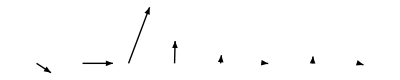
-Graphics-first layer row 4 @ 1 Pi/ 2, distance 0, input at nodes 2 and 3 from the left with an initial phase shift of pi/2

```mathematica
(*
arrowTbl=Table[Show[Labeled[Graphics[{Arrowheads[Small],Arrow[#]}&/@(arrows[[phase,All]])],"top layer column 3 @ "<>If[Not[IntegerQ[phaseLabels[[phase]]]],ToString[Numerator[phaseLabels[[phase]]]]<>" Pi/ "<>ToString[Denominator[phaseLabels[[phase]]]]<>", distance "<>ToString[dist],ToString[phaseLabels[[phase]]]<>" Pi, distance "<>If[phase<14,"2",If[phase<27,"1","0"]]]]],{phase,1,Dimensions[partitionedFitParameters][[1]]}]
*)
dist=0;
arrowTbl=Table[Show[Labeled[Graphics[{Arrowheads[Small],Arrow[#]}&/@(arrows)],"first layer row 4 @ "<>If[Not[IntegerQ[phaseLabels[[phase]]]],ToString[Numerator[phaseLabels[[phase]]]]<>" Pi/ "<>ToString[Denominator[phaseLabels[[phase]]]]<>", distance "<>ToString[dist],ToString[phaseLabels[[phase]]]<>" Pi, distance "<>If[phase<14,"2",If[phase<27,"1","0"]]]<>", input at nodes 2 and 3 from the left with an initial phase shift of pi/2"]],{phase,1,1}][[1]]
```

```mathematica
n=3.
{Cos[Mod[fitParameters[[n+1,2,2]]-fitParameters[[4,2,2]],2. Pi]],Sin[Mod[fitParameters[[n+1,2,2]]-fitParameters[[4,2,2]],2. Pi]]}
```

3.

{1.,0.}

```mathematica
degreeTable=Flatten[Table[m,{mm,1,3},{m,0,180,15}]]
```

{0,15,30,45,60,75,90,105,120,135,150,165,180,0,15,30,45,60,75,90,105,120,135,150,165,180,0,15,30,45,60,75,90,105,120,135,150,165,180}

```mathematica
Do[Export["D:\\GitHubDesktop\\eti\\Meeting_Material\\2022_09_01\\phase_series\\Distance_"<>If[q<14,"2",If[q<27,"1","0"]]<>"_Phase_"<>ToString[degreeTable[[q]]]<>".pdf",arrowTbl[[q]]],{q,1,39}]
```

Export::nodir: Directory D:\GitHubDesktop\eti\Meeting_Material\2022_09_01\phase_series\ does not exist.

Export::noopen: Cannot open D:\GitHubDesktop\eti\Meeting_Material\2022_09_01\phase_series\Distance_2_Phase_0.pdf.

Export::nodir: Directory D:\GitHubDesktop\eti\Meeting_Material\2022_09_01\phase_series\ does not exist.

Export::noopen: Cannot open D:\GitHubDesktop\eti\Meeting_Material\2022_09_01\phase_series\Distance_2_Phase_15.pdf.

Part::partw: Part 3 of  does not exist.

Export::nodir: Directory D:\GitHubDesktop\eti\Meeting_Material\2022_09_01\phase_series\ does not exist.

General::stop: Further output of Export::nodir will be suppressed during this calculation.

Export::noopen: Cannot open D:\GitHubDesktop\eti\Meeting_Material\2022_09_01\phase_series\Distance_2_Phase_30.pdf.

General::stop: Further output of Export::noopen will be suppressed during this calculation.

Part::partw: Part 4 of  does not exist.

Part::partw: Part 5 of  does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Dimensions[arrows]
```

{8,2,2}

```mathematica
Graphics[{Arrowheads[Small],Arrow[#]}&/@(arrows)]
```

-Graphics-

```mathematica
arrows[[1]]
```

{{0,0},{3.13637,-0.781429}}